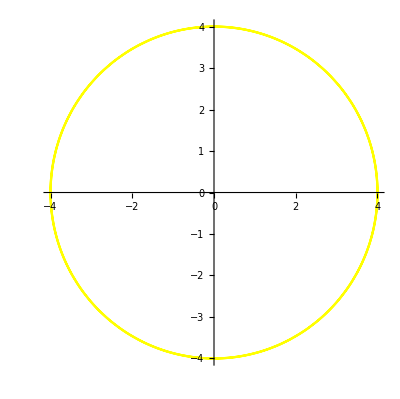

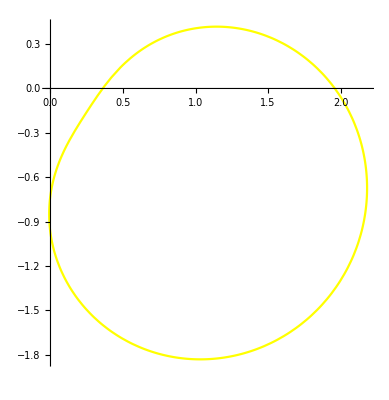

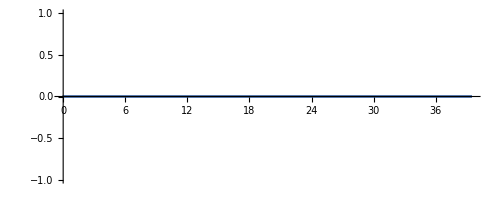

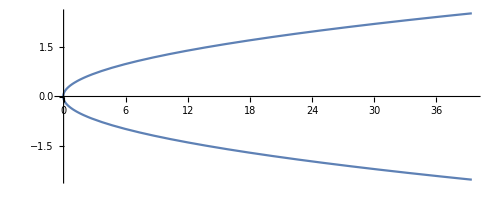

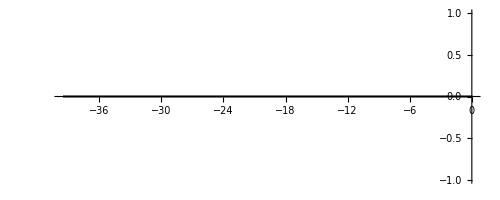

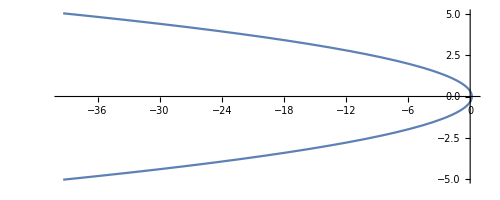

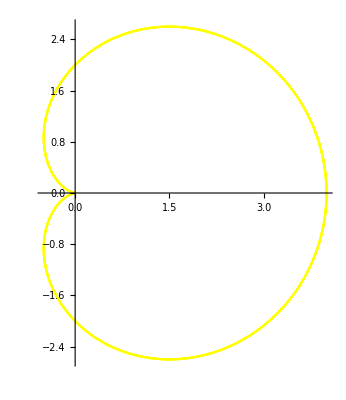

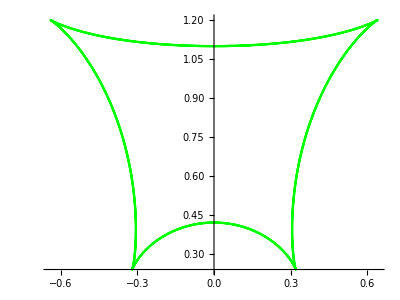

```mathematica
p1 = ParametricPlot[{((2Sin[u])^2-(2Cos[u])^2),8Sin[u]Cos[u]},{u,0,2Pi},PlotStyle->Yellow]
p2 = ParametricPlot[{(0.5Sin[u]+1)^2-(0.5Cos[u]-0.3)^2,2(0.5Cos[u]-0.3)(0.5Sin[u]+1)},{u,0,2Pi},PlotStyle->Yellow]
p3 = ParametricPlot[{u^2,0},{u,-2Pi,2Pi}]
p4 = ParametricPlot[{u^2-0.2^2,0.4u},{u,-2Pi,2Pi}]
p5 = ParametricPlot[{-u^2, 0},{u,-2Pi,2Pi}]
p6= ParametricPlot[{0.4^2-u^2,0.8u},{u,-2Pi,2Pi}]
p7= ParametricPlot[{(Sin[u]-1)^2-(Cos[u])^2,2Cos[u](Sin[u]-1)},{u,-2Pi,2Pi},PlotStyle->Yellow]
p8= ParametricPlot[{(0.4Sin[u]^3+0.6)^2-(0.4Cos[u]^3+0.6)^2,2(0.4Cos[u]^3+0.6)(0.4Sin[u]^3+0.6)},{u,-2Pi,2Pi},PlotStyle->Green]

p9= ParametricPlot[{(0.1(Cos [u]+ u Sin [u]))^2-(0.1(Sin [u] - u Cos[u]))^2,2(0.1(Cos [u]+ u Sin [u])0.1(Sin [u] - u Cos[u]))},{u,0,4Pi},PlotStyle->Green]
```

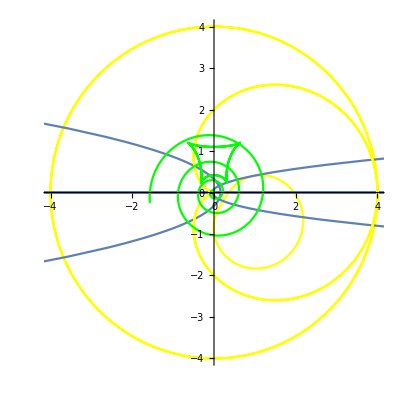

```mathematica
Show[p1, p2, p3, p4, p5, p6, p7, p8, p9]
```

```mathematica
p10= Manipulate[ParametricPlot[{{(a(Cos [u]+ u Sin [u]))^2-(a(Sin [u] - u Cos[ u]))^2,2a(Cos [u]+ u Sin [u])a(Sin [u] - u Cos[ u])},{(0.4Sin[u]^3+b)^2-(0.4Cos[u]^3+b^2)^2,2(0.4Sin[u]^3+b)(0.4Cos[u]^3+b^2)}}, {u,0,4Pi},PlotStyle->Green], {a, 0.01, 0.1}, {b, -0.4, 0.4}]
```

```mathematica
p11 = Manipulate[ParametricPlot[{{{(2Sin[u])^2-(2Cos[u])^2,8Cos[u]Sin[u]}},If[b=="Yes",{(0.5Sin[u]+1)^2-(0.5Cos[u]-0.3)^2,2(0.5Cos[u]-0.3)(0.5Sin[u]+1)}, {0, 0}]}, {u,0,len},PlotStyle->Yellow], {len, 0.01, 2Pi}, {b,{"Yes", "No"}}]
```

Выше был квадрат функций из задания функций. Ниже будет сопряженное, а экспоненты не будет

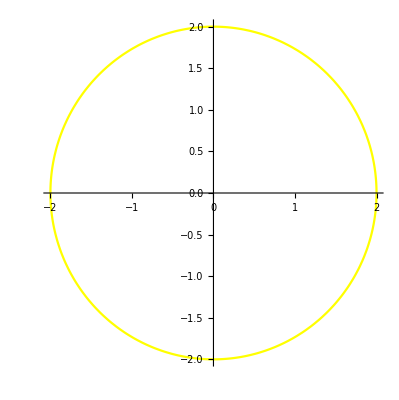

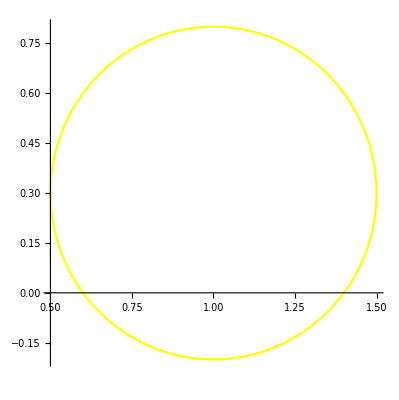

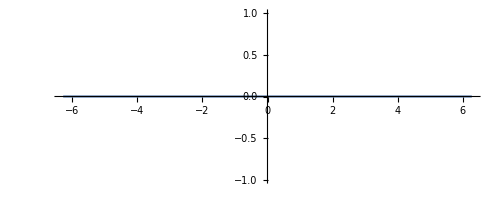

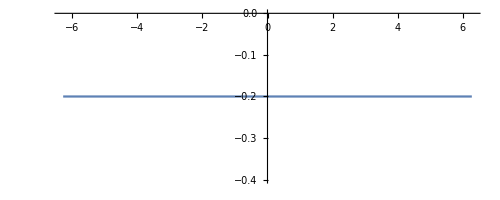

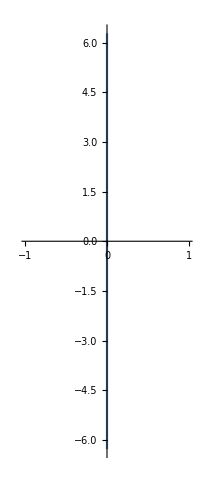

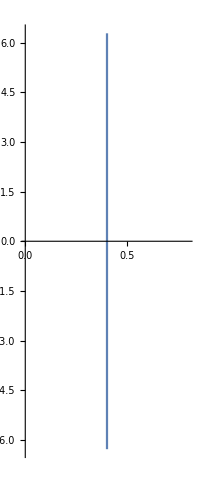

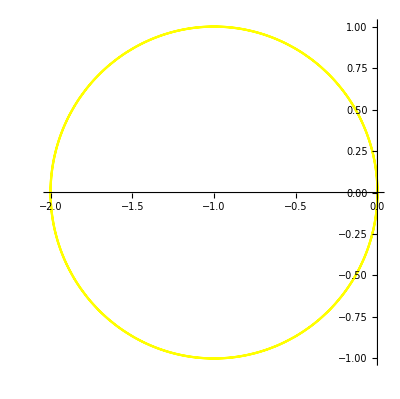

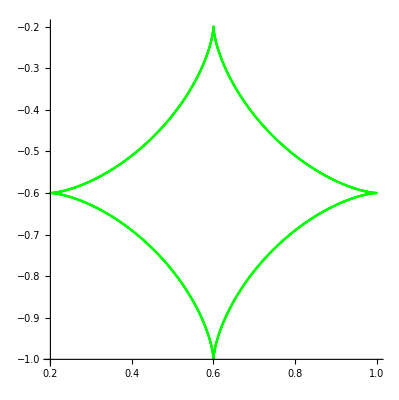

```mathematica
p1 = ParametricPlot[{2Sin[u],-2Cos[u]},{u,0,2Pi},PlotStyle->Yellow]
p2 = ParametricPlot[{0.5Sin[u]+1,-0.5Cos[u]+0.3},{u,0,2Pi},PlotStyle->Yellow]
p3 = ParametricPlot[{u,0},{u,-2Pi,2Pi}]
p4 = ParametricPlot[{u,-0.2},{u,-2Pi,2Pi}]
p5 = ParametricPlot[{0,-u},{u,-2Pi,2Pi}]
p6= ParametricPlot[{0.4,-u},{u,-2Pi,2Pi}]
p7= ParametricPlot[{Sin[u]-1,-Cos[u]},{u,-2Pi,2Pi},PlotStyle->Yellow]
p8= ParametricPlot[{0.4Sin[u]^3+0.6,-0.4Cos[u]^3-0.6},{u,-2Pi,2Pi},PlotStyle->Green]

p9= ParametricPlot[{0.1(Cos [u]+ u Sin [u]),-0.1(Sin [u] - u Cos[ u])},{u,0,4Pi},PlotStyle->Green]
```

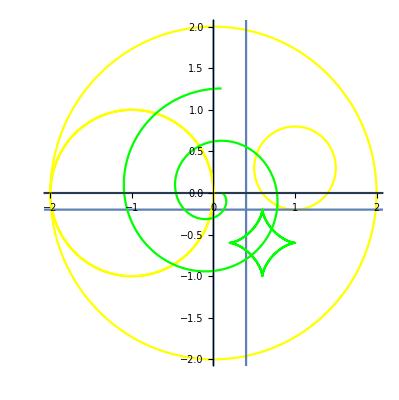

```mathematica
Show[p1, p2, p3, p4, p5, p6, p7, p8, p9]
```

```mathematica
p10= Manipulate[ParametricPlot[{{a(Cos [u]+ u Sin [u]),-a(Sin [u] - u Cos[ u])},{0.4Sin[u]^3+b,-0.4Cos[u]^3-b^2}}, {u,0,4Pi},PlotStyle->Green], {a, 0.01, 0.1}, {b, -0.4, 0.4}]
```

```mathematica
p11 = Manipulate[ParametricPlot[{{{2Sin[u],-2Cos[u]}},If[b=="Yes",{-0.5Sin[u]+1,+0.5Cos[u]+0.3}, {0, 0}]}, {u,0,len},PlotStyle->Yellow], {len, 0.01, 2Pi}, {b,{"Yes", "No"}}]
```